## bands

```mathematica
ass=Assumptions->{kx,ky,kz,k,θ,c,v0,ϕ,θp,ϕp,mbohr,μ,s} ∈ Reals && k>0 && kp>0 && 0<=θ<=π && 0<=θp<=π && c>0 && v0>0 && μ>0 && mbohr>0;
rep={kx->k Sin[θ] Cos[ϕ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]};
σ1=PauliMatrix[1];σ2=PauliMatrix[2];σ3=PauliMatrix[3];
Clear[ham];(* -Graphics- from https://doi.org/10.1038/s42005-021-00564-w*)
ham=c k^2 IdentityMatrix[2]+v0(kx σ1+ky σ2+ kz σ3)(*-mbohr kz σ3*);
FullSimplify[FullSimplify[Eigensystem[ham],ass]/.rep,ass]
```

{{k (c k-v0),k (c k+v0)},{{-ⅇ^(-ⅈ ϕ) Tan[θ/2],1},{ⅇ^(-ⅈ ϕ) Cot[θ/2],1}}}

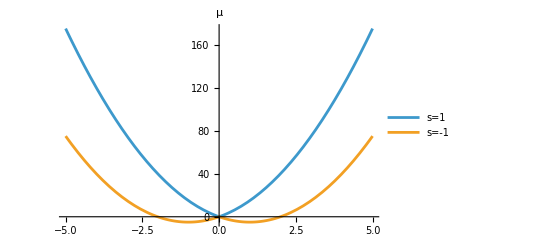

```mathematica
cval=5;v0val=2cval;
Plot[{Abs[k](cval Abs[k] +v0val),Abs[k](cval Abs[k] -v0val)},{k,-5,5},PlotLabel->Style["μ",10,Bold,FontFamily->"TexMaths Calligraphic"],PlotLegends->{"s=1","s=-1"}]
```

```mathematica
Clear[k,p,pl];
cval=50;v0val=0.1cval;k=√(kx^2+ky^2);lim=0.25;
style={Directive[Darker[Red](* s=1*),Opacity[0.75],Specularity[5]],Directive[Darker[Blue],Opacity[0.5],Specularity[5]]};

p=Plot3D[{k(cval k +v0val),k(cval k -v0val)},{kx,-lim,lim},{ky,-lim,lim},PlotStyle->style,Lighting->"Neutral",Ticks->False,Mesh->None,PlotPoints->200,BaseStyle->{FontFamily->"TexMaths Symbols",24,Black,Bold},LabelStyle->Black,Axes->True,AxesLabel->{"k_x","k_y","E"},AxesOrigin->{0,0,0},Boxed->False,ImageSize->300,BoxRatios->{1,1,1.1},ViewPoint->{-2.736532728062866,-1.9636593129724704,0.324700986782016},ImagePadding->{{20, 10}, {Automatic, 10}}];
Clear[k];
```

```mathematica
hp1=Hyperplane[{0,0,4},{0,1,1.5}];
g=Graphics3D[{ {Opacity[0.3],Yellow,hp1},Boxed->False}];

txt=Text[Style[" μ",30,Bold,Darker[Brown],FontFamily->"TexMaths Symbols"]];im=Rasterize[txt,ImageResolution->300,Background->None];pl=Show[{p,g}, PlotRange->{{-lim, lim},{-lim,lim},Automatic},Epilog->Inset[im,{0,0.35}],ImagePadding->{{20, 10}, {80, 0}}(* {{left,right},{bottom,top}}*)]
SetDirectory[NotebookDirectory[]];
Export["ksm.pdf",Rasterize[pl,ImageResolution-> 1000,RasterSize->1000],ImageSize->1000];
```

-Graphics3D-

## Fermi surfaces

```mathematica
Solve[k ( c k+s v0)==μ,k]/.s^2->1
```

{{k→(-s v0-√(v0^2+4 c μ))/(2 c)},{k→(-s v0+√(v0^2+4 c μ))/(2 c)}}

```mathematica
Clear[kF,B,c,ifun,v];


kF[B_,μ_,c_,v0_,s_,mbohr_,θ_,om_]:=Block[{e=1},

1/(12 c)(-4 s v0-(4 2^(2/3) (3 B c mbohr s-v0^2-3 c μ))/(18 B c mbohr v0-4 s v0^3-18 c s v0 μ-27 B c^2 e om v0 Cos[θ]+1/4 √(256 (3 B c mbohr s-v0^2-3 c μ)^3+16 v0^2 (2 s (-9 B c mbohr s+2 v0^2+9 c μ)+27 B c^2 e om Cos[θ])^2))^(1/3)+2 2^(1/3) (18 B c mbohr v0-4 s v0^3-18 c s v0 μ-27 B c^2 e om v0 Cos[θ]+1/4 √(256 (3 B c mbohr s-v0^2-3 c μ)^3+16 v0^2 (2 s (-9 B c mbohr s+2 v0^2+9 c μ)+27 B c^2 e om Cos[θ])^2))^(1/3))//Chop
];
```

```mathematica
5 10^0.1
```

6.29463

```mathematica
(*mu=15; cval= 5 10 ;v0val= 5 10^0.1; omval=1 ; bohrrm=0.45;bval= 10^-0.1;*)
mu=10.0^-1; cval=5 10^-2 ;v0val= 5 10^-3;  bohrrm= 3*10^-7 ;bval=20;
rot=-π/2;
thk=0.01;style={Directive[Darker[Red],Thickness[thk],Dashing[0.007],Opacity[0.5]],Directive[Darker[Blue],Thickness[thk],Dashing[0.01],Opacity[0.5]],(**)Directive[Darker[Red],Thickness[thk],Opacity[0.75]],Directive[Darker[Blue],Thickness[thk],Opacity[0.75]]};

a={Arrowheads[{0.1}],Arrow[{{-0.8,-0.4},{-0.8,0.4}}]};
txt=Text[Style["B",24,Bold,Black,FontFamily->"TexMaths Symbols"],{-0.8,0.45}];
arr=Graphics[{{Red,Thickness[0.01],a},txt},ImageSize->250];
omval=1;

pl=PolarPlot[{(√(v0val^2+4 cval mu)-v0val)/(2 cval),(√(v0val^2+4 cval mu)+v0val)/(2 cval),kF[bval,mu,cval,v0val,1,bohrrm,θ+rot,omval],kF[bval,mu,cval,v0val,-1,bohrrm,θ+rot,omval]},{θ,0,2π},PlotPoints->50,AspectRatio->1,AxesOrigin->{0,0},PlotStyle->style,PlotTheme->{"Detailed"},Ticks->None,BaseStyle->{FontFamily->"TexMaths Symbols",24,Black,Bold},LabelStyle->Black,Axes->True,AxesLabel->{"k_x","k_z"},PlotLegends->Placed[LineLegend[{"s=1, B=0","s=-1, B=0","s=1, B≠0","s=-1, B≠0"},LabelStyle->{FontFamily->"TexMaths Symbols",18,Bold,Darker[Brown]},LegendLayout->"Row"],Below](**),ImageSize->600]
```

-Graphics-

```mathematica
mu=15; cval= 5 10 ;v0val= 5 10^0.1; omval=1 ; bohrrm=0.45;bval= 10^-0.1;
rot=-π/2;lim=0.75;
thk=0.01;style={Directive[Darker[Red],Thickness[thk],Dashing[0.007],Opacity[0.5]],Directive[Darker[Blue],Thickness[thk],Dashing[0.01],Opacity[0.5]],(**)Directive[Darker[Red],Thickness[thk],Opacity[0.75]],Directive[Darker[Blue],Thickness[thk],Opacity[0.75]]};

a={Arrowheads[{0.1}],Arrow[{{-0.8,-0.4},{-0.8,0.4}}]};
txt=Text[Style["B",24,Bold,Black,FontFamily->"TexMaths Symbols"],{-0.8,0.45}];
arr=Graphics[{{Red,Thickness[0.01],a},txt},ImageSize->250];
omval=1;

pl=PolarPlot[{(√(v0val^2+4 cval mu)-v0val)/(2 cval),(√(v0val^2+4 cval mu)+v0val)/(2 cval),kF[bval,mu,cval,v0val,1,bohrrm,θ+rot,omval],kF[bval,mu,cval,v0val,-1,bohrrm,θ+rot,omval]},{θ,0,2π},PlotPoints->50,AspectRatio->1,AxesOrigin->{0,0},PlotStyle->style,PlotTheme->{"Detailed"},PlotRange->{{-lim,lim},{-lim,lim}},Ticks->None,BaseStyle->{FontFamily->"TexMaths Symbols",24,Black,Bold},LabelStyle->Black,Axes->True,AxesLabel->{"k_x","k_z"},PlotLegends->Placed[LineLegend[{"s=1, B=0","s=-1, B=0","s=1, B≠0","s=-1, B≠0"},LabelStyle->{FontFamily->"TexMaths Symbols",18,Bold,Darker[Brown]},LegendLayout->"Row"],Below](**),ImageSize->600];
pf=Show[{arr,pl},Ticks->None,BaseStyle->{FontFamily->"TexMaths Symbols",24,Black,Bold},LabelStyle->Black,Axes->True,AxesLabel->{"k_x","k_z"},PlotRange->{{-lim-0.1,lim},{-lim,lim}},ImageSize->400]
SetDirectory[NotebookDirectory[]];
Export["ksm2.pdf",Rasterize[pf,RasterSize->400],ImageSize->400];
```

-Graphics-